```mathematica
.6/1.8
```

0.333333

```mathematica
Integrate[.6a*E^(-2*t/3),t]
```

-0.9 a ⅇ^(-2 t/3)

```mathematica
%/(E^-2t/3)
```

-(2.7 a ⅇ^(2-(2 t)/3))/t

```mathematica
DSolve[{A'[t]==0.6*a*E^(-t)-A[t]/3,A[0]==0},A[t],t]
```

{{A[t]→0.9 a ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t))}}

```mathematica
AforPlots=Table[0.8999999999999998 a ⅇ^(-1.3333333333333333 t) (-1. ⅇ^(0.3333333333333333 t)+1. ⅇ^(1. t)),{a,.5,10,.5}]
```

{0.45 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),0.9 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),1.35 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),1.8 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),2.25 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),2.7 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),3.15 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),3.6 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),4.05 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),4.5 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),4.95 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),5.4 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),5.85 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),6.3 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),6.75 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),7.2 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),7.65 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),8.1 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),8.55 ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t)),9. ⅇ^(-1.33333 t) (-1. ⅇ^(0.333333 t)+1. ⅇ^(1. t))}

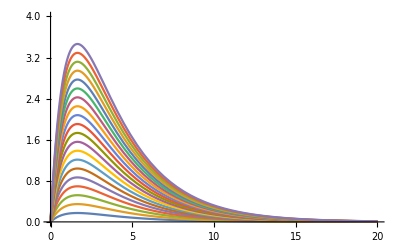

```mathematica
Plot[AforPlots,{t,0,20},PlotRange->{{0,20},{0,4}}]
```